# FD Formulas

```mathematica
ClearAll[grid,size,order];
size=3;
order=2;
grid={Table[i,{i,-size,size}]dx,Table[i,{i,-size,size}]dy,Table[i,{i,-size,size}]dz};

ClearAll[values];
values=Flatten[Table[F[a,b,c],{a,grid⟦1⟧},{b,grid⟦2⟧},{c,grid⟦3⟧}]];

ClearAll[gradient];
gradient={
FullSimplify[NDSolve`FiniteDifferenceDerivative[Derivative[1,0,0],grid,values,"DifferenceOrder"->order]⟦Position[values,F[0,0,0]]⟦1,1⟧⟧],
FullSimplify[NDSolve`FiniteDifferenceDerivative[Derivative[0,1,0],grid,values,"DifferenceOrder"->order]⟦Position[values,F[0,0,0]]⟦1,1⟧⟧],
FullSimplify[NDSolve`FiniteDifferenceDerivative[Derivative[0,0,1],grid,values,"DifferenceOrder"->order]⟦Position[values,F[0,0,0]]⟦1,1⟧⟧]
};


ClearAll[hessian];
hessian={
FullSimplify[NDSolve`FiniteDifferenceDerivative[Derivative[2,0,0],grid,values,"DifferenceOrder"->order]⟦Position[values,F[0,0,0]]⟦1,1⟧⟧],
FullSimplify[NDSolve`FiniteDifferenceDerivative[Derivative[1,1,0],grid,values,"DifferenceOrder"->order]⟦Position[values,F[0,0,0]]⟦1,1⟧⟧],
FullSimplify[NDSolve`FiniteDifferenceDerivative[Derivative[1,0,1],grid,values,"DifferenceOrder"->order]⟦Position[values,F[0,0,0]]⟦1,1⟧⟧],

FullSimplify[NDSolve`FiniteDifferenceDerivative[Derivative[0,2,0],grid,values,"DifferenceOrder"->order]⟦Position[values,F[0,0,0]]⟦1,1⟧⟧],
FullSimplify[NDSolve`FiniteDifferenceDerivative[Derivative[0,1,1],grid,values,"DifferenceOrder"->order]⟦Position[values,F[0,0,0]]⟦1,1⟧⟧],

FullSimplify[NDSolve`FiniteDifferenceDerivative[Derivative[0,0,2],grid,values,"DifferenceOrder"->order]⟦Position[values,F[0,0,0]]⟦1,1⟧⟧]
};

ClearAll[F];
F[a_,b_,c_]:=u[pI+a/dx*pDI0+b/dy*pDI1+c/dz*pDI2];

ClearAll[rules];
rules={"pI"->"p.I","pDI0"->"p.DI[0]","pDI1"->"p.DI[1]","pDI2"->"p.DI[2]","dx"->"p.DX[0]","dy"->"p.DX[1]","dz"->"p.DX[2]","Power"->"pow"};

"duda = "<>StringReplace[ToString[gradient⟦1⟧,CForm],rules]
"dudb = "<>StringReplace[ToString[gradient⟦2⟧,CForm],rules]
"dudc = "<>StringReplace[ToString[gradient⟦3⟧,CForm],rules]

"d2udada = "<>StringReplace[ToString[hessian⟦1⟧,CForm],rules]
"d2udadb = "<>StringReplace[ToString[hessian⟦2⟧,CForm],rules]
"d2udadc = "<>StringReplace[ToString[hessian⟦3⟧,CForm],rules]

"d2udbdb = "<>StringReplace[ToString[hessian⟦4⟧,CForm],rules]
"d2udbdc = "<>StringReplace[ToString[hessian⟦5⟧,CForm],rules]

"d2udcdc = "<>StringReplace[ToString[hessian⟦6⟧,CForm],rules]
```

duda = (-u(-p.DI[0] + p.I) + u(p.DI[0] + p.I))/(2.*p.DX[0])

dudb = (-u(-p.DI[1] + p.I) + u(p.DI[1] + p.I))/(2.*p.DX[1])

dudc = (-u(-p.DI[2] + p.I) + u(p.DI[2] + p.I))/(2.*p.DX[2])

d2udada = (-2*u(p.I) + u(-p.DI[0] + p.I) + u(p.DI[0] + p.I))/pow(p.DX[0],2)

d2udadb = (u(-p.DI[0] - p.DI[1] + p.I) - u(p.DI[0] - p.DI[1] + p.I) - u(-p.DI[0] + p.DI[1] + p.I) + u(p.DI[0] + p.DI[1] + p.I))/(4.*p.DX[0]*p.DX[1])

d2udadc = (u(-p.DI[0] - p.DI[2] + p.I) - u(p.DI[0] - p.DI[2] + p.I) - u(-p.DI[0] + p.DI[2] + p.I) + u(p.DI[0] + p.DI[2] + p.I))/(4.*p.DX[0]*p.DX[2])

d2udbdb = (-2*u(p.I) + u(-p.DI[1] + p.I) + u(p.DI[1] + p.I))/pow(p.DX[1],2)

d2udbdc = (u(-p.DI[1] - p.DI[2] + p.I) - u(p.DI[1] - p.DI[2] + p.I) - u(-p.DI[1] + p.DI[2] + p.I) + u(p.DI[1] + p.DI[2] + p.I))/(4.*p.DX[1]*p.DX[2])

d2udcdc = (-2*u(p.I) + u(-p.DI[2] + p.I) + u(p.DI[2] + p.I))/pow(p.DX[2],2)

# Projections

```mathematica
ClearAll[Jac,DJac];
Jac=FullSimplify[Table[D[ai,xi],{ai,{a[x,y,z],b[x,y,z],c[x,y,z]}},{xi,{x,y,z}}]];
DJac=FullSimplify[Table[D[ai,xi,xj],{ai,{a[x,y,z],b[x,y,z],c[x,y,z]}},{xi,{x,y,z}},{xj,{x,y,z}}]];

ClearAll[ldu,ld2u];
ldu=FullSimplify[Table[D[u[a,b,c],i],{i,{a,b,c}}]];
ld2u=FullSimplify[Table[D[u[a,b,c],i,j],{i,{a,b,c}},{j,{a,b,c}}]];

ClearAll[gdu,gd2u];
gdu=FullSimplify[Table[Sum[Jac⟦i,k⟧ldu⟦i⟧,{k,1,3}],{i,1,3}]];
gd2u=FullSimplify[Table[Sum[Jac⟦k,i⟧DJac⟦k,l,j⟧ldu⟦l⟧,{k,1,3},{l,1,3}]+Sum[Jac⟦k,i⟧Jac⟦l,j⟧ld2u⟦k,l⟧,{k,1,3},{l,1,3}],{i,1,3},{j,1,3}]];

ClearAll[rules];
rules=
Join[
Flatten[Table[ToString[D[u[a,b,c],i],CForm]->"dud"<>ToString[i],{i,{a,b,c}}]],
Flatten[Table[ToString[D[u[a,b,c],i,j],CForm]->"d2ud"<>ToString[i]<>"d"<>ToString[j],{i,{a,b,c}},{j,{a,b,c}}]],
Flatten[Table[ToString[D[ai,xi],CForm]->"vJ_d"<>ToString[Head[ai]]<>"_d"<>ToString[xi]<>"(p.I)",{ai,{a[x,y,z],b[x,y,z],c[x,y,z]}},{xi,{x,y,z}}]],
Flatten[Table[ToString[D[ai,xi,xj],CForm]->"vdJ_d2"<>ToString[Head[ai]]<>"_d"<>ToString[xi]<>"d"<>ToString[xj]<>"(p.I)",{ai,{a[x,y,z],b[x,y,z],c[x,y,z]}},{xi,{x,y,z}},{xj,{x,y,z}}]],
{"Power"->"pow"}
];

"dudx = "<>StringReplace[ToString[gdu⟦1⟧,CForm],rules]
"dudy = "<>StringReplace[ToString[gdu⟦2⟧,CForm],rules]
"dudz = "<>StringReplace[ToString[gdu⟦3⟧,CForm],rules]

"dudxdx = "<>StringReplace[ToString[gd2u⟦1,1⟧,CForm],rules]
"dudydy = "<>StringReplace[ToString[gd2u⟦2,2⟧,CForm],rules]
"dudzdz = "<>StringReplace[ToString[gd2u⟦3,3⟧,CForm],rules]
```

dudx = (vJ_da_dz(p.I) + vJ_da_dy(p.I) + vJ_da_dx(p.I))*duda

dudy = dudb*(vJ_db_dz(p.I) + vJ_db_dy(p.I) + vJ_db_dx(p.I))

dudz = dudc*(vJ_dc_dz(p.I) + vJ_dc_dy(p.I) + vJ_dc_dx(p.I))

dudxdx = d2udbdb*pow(vJ_db_dx(p.I),2) + 2*d2udbdc*vJ_db_dx(p.I)*vJ_dc_dx(p.I) + d2udcdc*pow(vJ_dc_dx(p.I),2) + dudc*(vJ_da_dx(p.I)*vdJ_d2a_dxdz(p.I) + vJ_db_dx(p.I)*vdJ_d2b_dxdz(p.I)) + dudc*vJ_dc_dx(p.I)*vdJ_d2c_dxdz(p.I) + 2*vJ_da_dx(p.I)*vJ_dc_dx(p.I)*d2udadc + dudb*vJ_da_dx(p.I)*vdJ_d2a_dxdy(p.I) + dudb*vJ_db_dx(p.I)*vdJ_d2b_dxdy(p.I) + dudb*vJ_dc_dx(p.I)*vdJ_d2c_dxdy(p.I) + 2*vJ_da_dx(p.I)*vJ_db_dx(p.I)*d2udadb + vJ_da_dx(p.I)*duda*vdJ_d2a_dxdx(p.I) + vJ_db_dx(p.I)*duda*vdJ_d2b_dxdx(p.I) + vJ_dc_dx(p.I)*duda*vdJ_d2c_dxdx(p.I) + pow(vJ_da_dx(p.I),2)*d2udada

dudydy = d2udcdc*pow(vJ_dc_dy(p.I),2) + dudc*(vJ_da_dy(p.I)*vdJ_d2a_dydz(p.I) + vJ_db_dy(p.I)*vdJ_d2b_dydz(p.I) + vJ_dc_dy(p.I)*vdJ_d2c_dydz(p.I)) + 2*vJ_db_dy(p.I)*vJ_dc_dy(p.I)*d2udbdc + vJ_da_dy(p.I)*dudb*vdJ_d2a_dydy(p.I) + vJ_db_dy(p.I)*dudb*vdJ_d2b_dydy(p.I) + vJ_dc_dy(p.I)*dudb*vdJ_d2c_dydy(p.I) + pow(vJ_db_dy(p.I),2)*d2udbdb + 2*vJ_da_dy(p.I)*vJ_dc_dy(p.I)*d2udadc + vJ_da_dy(p.I)*duda*vdJ_d2a_dxdy(p.I) + vJ_db_dy(p.I)*duda*vdJ_d2b_dxdy(p.I) + vJ_dc_dy(p.I)*duda*vdJ_d2c_dxdy(p.I) + 2*vJ_da_dy(p.I)*vJ_db_dy(p.I)*d2udadb + pow(vJ_da_dy(p.I),2)*d2udada

dudzdz = pow(vJ_db_dz(p.I),2)*d2udbdb + vJ_db_dz(p.I)*(dudc*vdJ_d2b_dzdz(p.I) + dudb*vdJ_d2b_dydz(p.I) + 2*vJ_dc_dz(p.I)*d2udbdc + duda*vdJ_d2b_dxdz(p.I)) + vJ_dc_dz(p.I)*(dudc*vdJ_d2c_dzdz(p.I) + vJ_dc_dz(p.I)*d2udcdc + dudb*vdJ_d2c_dydz(p.I) + duda*vdJ_d2c_dxdz(p.I)) + vJ_da_dz(p.I)*(dudc*vdJ_d2a_dzdz(p.I) + dudb*vdJ_d2a_dydz(p.I) + duda*vdJ_d2a_dxdz(p.I) + 2*vJ_dc_dz(p.I)*d2udadc + 2*vJ_db_dz(p.I)*d2udadb) + pow(vJ_da_dz(p.I),2)*d2udada

# Derivatives of standing wave ID

## Definitions

```mathematica
ClearAll[seismicColors];
seismicColors[x_?NumericQ]/;0≤x≤1:=Blend[{RGBColor[0.,0.,0.3],RGBColor[0.,0.,1.],RGBColor[1.,1.,1.],RGBColor[1.,0.,0.],RGBColor[0.5,0.,0.]},x]

ClearAll[pts];
pts=30;
```

## Standing wave function

```mathematica
ClearAll[standingWave];
standingWave[A_,kx_,ky_,kz_,t_,x_,y_,z_]:=Module[
{ω},
ω=√(kx^2+ky^2+kz^2);
Return[A*Cos[2π*ω*t]*Cos[2*π*kx*x]*Cos[2π*ky*y]*Cos[2*π*kz*z]];
];

ClearAll[u,rho];
u=standingWave[1,1/2,1/2,1/2,t,x,y,z];
rho=D[u,t];

ClearAll[uRHS,rhoRHS];
uRHS=rho;
rhoRHS=D[u,{x,2}]+D[u,{y,2}]+D[u,{z,2}];
```

## State plots

### u

```mathematica
ClearAll[uPlot];
uPlot=DensityPlot[
u//.{t->0,z->0},

{x,-11,11},
{y,-11,11},

PlotPoints->pts,
PlotLegends->Automatic,
ColorFunction->seismicColors,
RegionFunction->Function[{x,y,z},√(x^2+y^2)≤11],

ImageSize->Large,
PlotRange->Full
];
```

### rho

```mathematica
ClearAll[rhoPlot];
rhoPlot=DensityPlot[
rho//.{t->0,z->0},

{x,-11,11},
{y,-11,11},

PlotPoints->pts,
PlotLegends->Automatic,
ColorFunction->seismicColors,
RegionFunction->Function[{x,y,z},√(x^2+y^2)≤11],

ImageSize->Large,
PlotRange->Full
];
```

### Plots

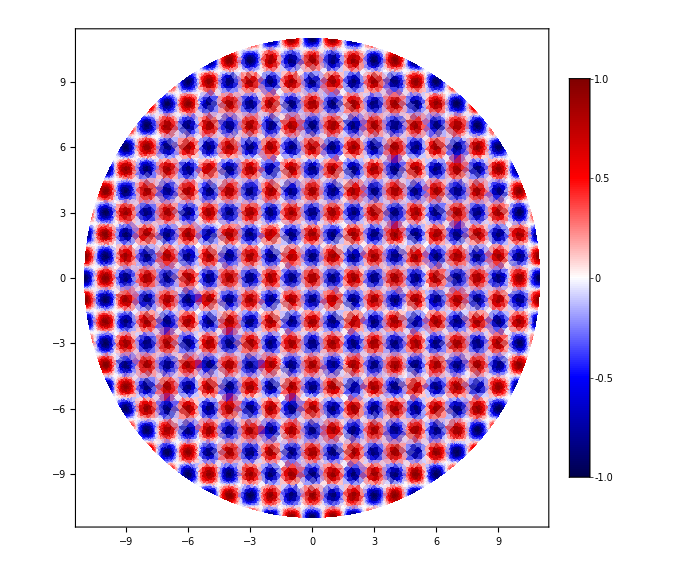
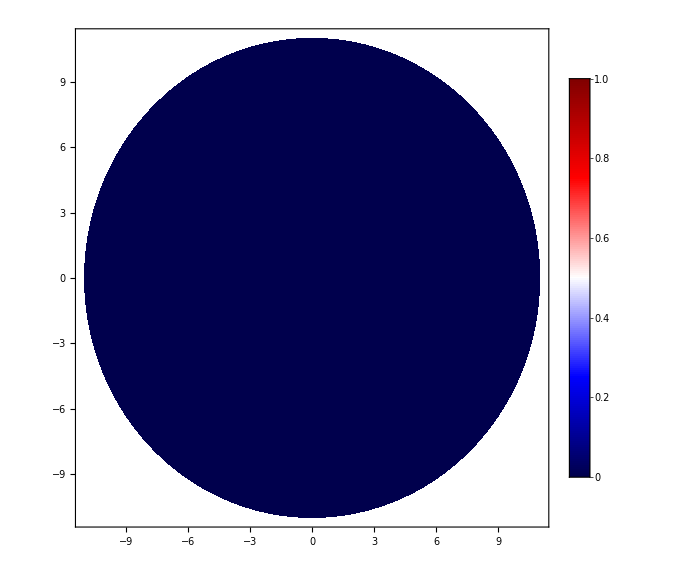

```mathematica
Row[{uPlot,rhoPlot}]
```

## RHS plots

### uRHS

```mathematica
ClearAll[uRHSPlot];
uRHSPlot=DensityPlot[
uRHS//.{t->0,z->0},

{x,-11,11},
{y,-11,11},

PlotPoints->pts,
PlotLegends->Automatic,
ColorFunction->seismicColors,
RegionFunction->Function[{x,y,z},√(x^2+y^2)≤11],

ImageSize->Large,
PlotRange->Full
];
```

### rhoRHS

```mathematica
ClearAll[rhoRHSPlot];
rhoRHSPlot=DensityPlot[
rhoRHS//.{t->0,z->0},

{x,-11,11},
{y,-11,11},

PlotPoints->pts,
PlotLegends->Automatic,
ColorFunction->seismicColors,
RegionFunction->Function[{x,y,z},√(x^2+y^2)≤11],

ImageSize->Large,
PlotRange->Full
];
```

### Plots

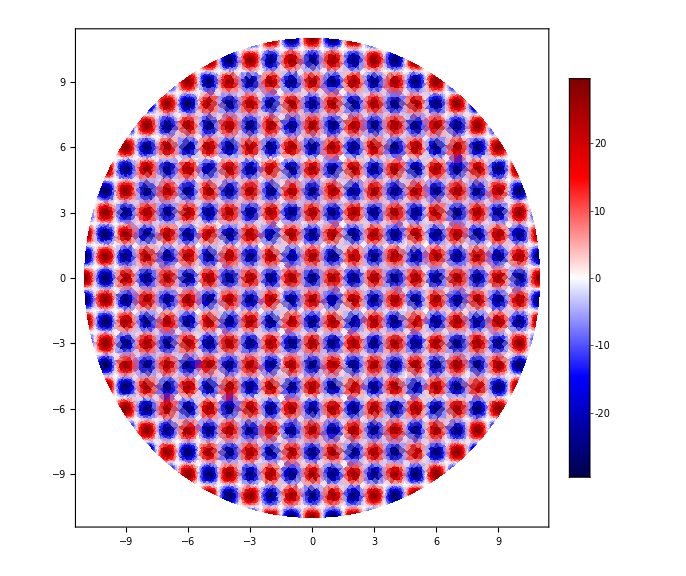
-Graphics--Graphics-

```mathematica
Row[{uRHSPlot,rhoRHSPlot}]
```